```mathematica
CleanSlate;
$MinPrecision=MachinePrecision;
  ρz[z_] := z/(1 + Sqrt[1 - z])^2; 
 ρzb[z_] := ρz[Conjugate[z]]; 
 (*error estimates*)
    ρintErrorEstimateG[d_, DDs_, z_, γ_] := (2^(γ + 4*d)*β^(γ - 4*d)*Gamma[1 - γ + 4*d, β*DDs])/(Gamma[1 - γ + 4*d]*(1 - r^2)^γ)/.  {r -> Abs[ρz[z]], β -> -Log[Abs[ρz[z]]]}; 
      ρintErrorEstimateFt[d_, DDs_, z_, γ_] := 
     v^d*ρintErrorEstimateG[d, DDs, z, γ] + u^d*ρintErrorEstimateG[d, DDs, 1 - z, γ] /. {u -> z*Conjugate[z], v -> (1 - z)*(1 - Conjugate[z])}; 
     (*coefficients and prefactors*)
    kfunctAna[β_, x_] := Exp[(β/2)*Log[4*((1 - Sqrt[1 - x])^2/x)]]*(x/(2*(1 - x)^(1/4)*(1 - Sqrt[1 - x]))); 
    ConformalBlockAna[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunctAna[DD + l, z]*kfunctAna[DD - l - 2, Conjugate[z]] - 
       kfunctAna[DD + l, Conjugate[z]]*kfunctAna[DD - l - 2, z]);
       (*derivatives*)
       FAnaDer[DD_, l_, z_] := (1/(z - Conjugate[z]))*(-1)^(2*l)*(1 - z)*z*
      (1 - Conjugate[z])*Conjugate[z]*(-((2^(-5 + 2*DD)*((1 - Sqrt[z])/(1 + Sqrt[z]))^((1/2)*(-2*l + DD))*(1 - z)*
          ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^((1/2)*(-2*l + DD))*(-((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - 
           Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
           ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l) + (((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + 
             Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
             ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l))*Sqrt[Conjugate[z]])*(1 - Conjugate[z])*
          (Log[16] + Log[-((-1 + Sqrt[z])/(1 + Sqrt[z]))] + Log[-((-1 + Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))]))/
         ((-1 + Sqrt[z])^2*z^(1/4)*(-1 + Sqrt[Conjugate[z]])^2*Conjugate[z]^(1/4))) + (2^(-5 + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-2*l + DD))*z*
         ((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^((1/2)*(-2*l + DD))*Conjugate[z]*(-2*z*(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l)*
           (-1 + Sqrt[1 - Conjugate[z]]) + Conjugate[z]*(2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l) + 
            z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l) + (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l))))*
         (Log[16] + Log[(-1 + Sqrt[1 - z])^2/z] + Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*
         (-1 + Sqrt[1 - Conjugate[z]])^3*(1 - Conjugate[z])^(1/4))); 
	 ConformalBlockAnaDer[DD_, l_, z_] := 
     -((I*(-1)^l*2^(-6 - l + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-l + DD))*Abs[z]^4*((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^
         ((1/2)*(-l + DD))*(2*z*(-1 + Sqrt[1 - Conjugate[z]])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l + 
         Conjugate[z]*(-2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + 
             (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l)))*(Log[(16*(-1 + Sqrt[1 - z])^2)/z] + 
         Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*(-1 + Sqrt[1 - Conjugate[z]])^3*
        (1 - Conjugate[z])^(1/4)*Im[z])); 
	kfunct[β_, x_] := kfunct[β, x] = x^(β/2)*Hypergeometric2F1[β/2, β/2, β, x]; 
    ConformalBlock[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunct[DD + l, z]*kfunct[DD - l - 2, Conjugate[z]] - 
       kfunct[DD + l, Conjugate[z]]*kfunct[DD - l - 2, z]); 
      
      (*random sample of z around (1/2+I0)*)
           Sample[nz_,var_,seed_] := Module[{imax}, SeedRandom[seed];Table[Abs[RandomVariate[NormalDistribution[0, var]]]+
           1/2+I Abs[RandomVariate[NormalDistribution[0, var]]],{imax,1,nz}]]; 
(*Exponential factor to renormalize*)
dimExpFactor[a_,b_]:=Log[4(1-Sqrt[1/2 -a -b])^2/(1/2 + a +b)];

renomFactor[dim_]:=Exp[-(dim-1)dimExpFactor[0,0]];
(*renomFactor[dim_]:=1;*)
(*Conformal Blocks*)
qQGen[Δϕ_,Δ_,L_,zsample_]:=renomFactor[Δ] (((1 - zsample)*(1 - Conjugate[zsample]))^Δϕ    ConformalBlock[Δ, L , zsample]- ((zsample)*( Conjugate[zsample]))^Δϕ ConformalBlock[Δ, L,1- zsample])2^(L);
qQGenDims[Δϕ_,ΔL_,z_]:=qQGen[1,#1[[1]],#1[[2]], z]&/@ΔL

(*Nice action functional*)
chi2Functional[qq0_,id_,w_,rhovec_]:=Block[{nu,s,r},
nu = Dimensions[w][[1]]-Length[rhovec];
r=(qq0.rhovec-id);
s=r.w.r;
Return[s/nu]];

(*Metropolis MC routine*)
MetroGoFixedSelectiveDir[Δϕ_,ΔLOriginal_,Ndit_,prec_,betad_,seed_,sigmaMC_,dcross_,lmax_,idTag_,initialOps_]:=Block[{itd, DDldata, sigmaz, sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, Nz, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    IdsampleEx,zOPE,QQOPE,Calc,coeffTemp,Ident,OPEcoeff,ActionTot,  TotD ,DDldataold,QQold,ΔLOld,dimToVary,PP,QQsave,ΔL,dw,smearedaction}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
    Nz=Length[ΔLOriginal]+1;
  zsample = Sample[Nz,1/100,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
     
    (*Monte Carlo Iteration*)
TotD =   Reap[ Do[
$MinPrecision=prec;
          ΔLOld=ΔL;
          QQold=QQ0;  

(*let every successive run start by varying only the new operator*)
        If[it<Ndit/10&& Nz!=initialOps+1,dimToVary=Nz-1,  dimToVary = RandomInteger[{1,lmax}]];
       (*Shift one dimension by a random amount*)       
          ΔL[[dimToVary,1]] = ΔL[[dimToVary,1]]+ RandomVariate[NormalDistribution[0, sigmaMC]];
(*Reevaluate coefficients*)
           QQ0[[dimToVary]] = qQGen[Δϕ,ΔL[[dimToVary]][[1]],ΔL[[dimToVary]][[2]],zsample];
          
    (*Coefficients for LES and action thence*)
          PP = Join[QQ0, {Idsample}]; 
          Actionnew = Log[Det[PP]^2]; 
QQsave=QQ0;
(*Brot noch schmieren? *)
smearedaction=Reap[Table[
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]+dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]-dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];QQ0=QQsave;,{dimToVary,1,lmax}]];

 Actionnew =Actionnew +Total[smearedaction[[2]]//Flatten] ;
         

          metcheck = Exp[(-betad)*(Actionnew - Action)];
          rr = RandomReal[{0, 1}];
          If[metcheck>rr, Action = Actionnew,ΔL=ΔLOld;QQ0=QQold];
          
$MinPrecision=10;
   dw=ΔL[[All,1]];
          Sow[ {it, dw, N[Action,10]}],
     {it, 1, Ndit}]]; 
$MinPrecision=3;
      Export["Res-fixed_Param_Nit="<>ToString[Ndit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[betad,3]]<>"sigmaMC="<>ToString[N[sigmaMC,3]]<>"dcross="<>ToString[N[dcross,3]]<>"seed="<>ToString[seed]<>"id="<>idTag<>".txt", TotD[[2]]];]

weightedLeastSquares[qq0_,id_,w_]:=Block[{rhovec,nu,s,r},
rhovec=Inverse[Transpose[qq0].w.qq0].Transpose[qq0] . w.id;
nu = Dimensions[w][[1]]-Length[rhovec];
r=(qq0.rhovec-id);
s=r.w.r;
Return[{rhovec,(Diagonal[Inverse[Transpose[qq0].w.qq0]])^(-1/2), s/nu}]];

metroReturnAvg[prec_,nit_,β_,ΔL_,seed_,initialOps_,idtag_]:=Block[{data},
MetroGoFixedSelectiveDir[1,ΔL,nit,prec,β,seed,1/10,1/3,Length[ΔL],ToString[Length[ΔL]]<>"id"<>idtag,initialOps];
data= Get["Res-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".txt"];
Export["Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]],{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
Export["zoom-Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]]-2i+1,{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotRange->{{0,nit},{0,2}},PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
{Mean[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]],StandardDeviation[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]]}]

checkMetroWeighted[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
finalcheck=Abs[results[[1]].QQ0-Idsample]<errSample//Thread;
Return[{results,And@@finalcheck}];
]
mcIterator[initialOps_,finalOps_,ΔLinitial_,β_,nz_,prec_,seed_,nits_,runid_]:=Block[{ΔL=ΔLinitial,results},
results=Reap[Table[ΔL[[1;;it,1]]=Sow[metroReturnAvg[prec,nits[[it-initialOps+1]],β[[it-initialOps+1]],ΔL[[1;;it]],seed,initialOps,runid]][[1]];
Sow[checkMetroWeighted[1,ΔL[[1;;it]],prec,seed,nz,runid]];
,{it,initialOps,finalOps}]];
Export["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt", results];
]
mcPlotDimsAndOPEs[initialOps_,finalOps_,nz_,prec_,seed_,runid_]:=Block[{data,dims,opes,mcDims,mcOpes,refDims,refOpes,nrecs=(finalOps-initialOps) +1},
data= Get["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt"];
dims=data[[1,Range[1,2nrecs -1,2]]];
opes=data[[1,Range[2,2nrecs ,2]]];
mcDims=ListPlot[dims[[;;,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refDims=Plot[{2,4,6,8},{x,0,nrecs},PlotStyle->Dashed];
mcOpes=ListPlot[opes[[;;,1,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refOpes=Plot[{2,1/3},{x,0,nrecs},PlotStyle->Dashed];
Export["dims-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcDims,refDims],PlotLabel->"Dims_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Export["opes-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcOpes,refOpes],PlotLabel->"OPEs_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Return[opes[[;;,2]]]
]
deltaFree[n_]:={2#,2#-2}&/@Range[1,n,1];
opeFreeRen[n_]:=(renomFactor[2#])^(-1) 2((2#-2)!)^2/(2(2#-2))!&/@Range[1,n,1];
(*deltascanner*)
checkMetroWScan[Δϕ_,ΔLOriginal_,prec_,seed_,nZ_,sigmaz_,dimToVary_,x_]:=Block[{ΔL=ΔLOriginal}, 
(* ΔL[[5,1]] = SetPrecision[ΔL[[5,1]]+ 5/100000,prec];*)
 ΔL[[dimToVary,1]] = SetPrecision[ΔL[[dimToVary,1]]+ x,prec];
checkMetroWeighted[Δϕ,ΔL,prec,seed,nZ,sigmaz]
]

(*OPE dependence exploration*)
opeCoeffDependencePlotter[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_,rhoexp_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample,rhoarray}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
rhoarray=Table[results[[1]],{i,1,21}];
rhoarray[[;;,rhoexp]]=(rhoarray[[#,rhoexp]](1+(#-11)/1000000))&/@Range[1,21];
{rhoarray[[;;,rhoexp]]-results[[1,rhoexp]],chi2Functional[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)],#]&/@rhoarray}//Transpose
]
biDimChi2DependencePlotter[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_,range_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample,deltaArray}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
ContourPlot[ΔL[[1,1]]=2+x;ΔL[[2,1]]=4+y;QQ0 = qQGenDims[Δϕ,ΔL,zsample];chi2Functional[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)],results[[1]]],{x,-range,range},{y,-range/1000,range/1000},PlotLegends->Automatic]
]
biDimChi2DependenceDataGen[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_,range_,npoints_,opstovary_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample,deltaArray}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
ParallelTable[{ΔL[[opstovary[[1]],1]]=ΔLOriginal[[opstovary[[1]],1]]+x range/npoints, ΔL[[opstovary[[2]],1]]=ΔLOriginal[[opstovary[[2]],1]]+ y  range/npoints, QQ0[[opstovary]] = qQGenDims[Δϕ,ΔL[[opstovary]],zsample];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];chi2Functional[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)],results[[1]]]},{x,-npoints,npoints},{y,-npoints,npoints}]
]
```

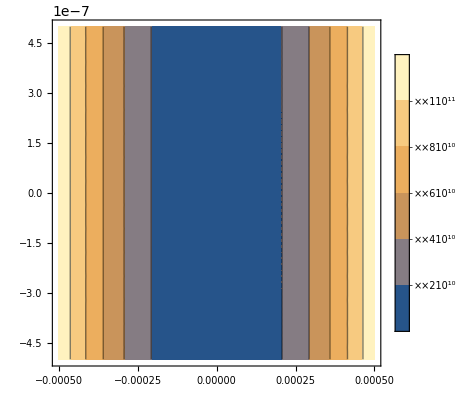

```mathematica
biDimChi2DependencePlotter[1,deltaFree[10],90,123,1000,10^(-1),1/2000]
```

```mathematica
(b=2+#; Sin[b])&/@Range[0,1]
```

{Sin[2],Sin[3]}

```mathematica
a=Flatten[biDimChi2DependenceDataGen[1,deltaFree[10],90,123,1200,10^(-1),1/500,30,{1,2}]//Chop,1];
Export["data-correct-2n4-zoommm.tsv",a]
```

data-correct-2n4-zoommm.tsv

```mathematica
b=Flatten[biDimChi2DependenceDataGen[1,deltaFree[10],90,123,1200,10^(-1),1/50,40,{3,4}]//Chop,1];
Export["data-correct-6n8-smooth.tsv",b]
```

data-correct-6n8-smooth.tsv

```mathematica
a2=a;
```

```mathematica
b2=b;
```

```mathematica
b[[;;,3]]=b[[;;,3]]//Log;
```

```mathematica
ListPlot3D[a]
```

-Graphics3D-

-Graphics3D-

```mathematica
Export["data-correct-4n6-zoom.tsv",a]
```

data-correct-4n6-zoom.tsv

```mathematica
Flatten[a,1]//Dimensions
```

{441,3}

```mathematica
Export["data.tsv",Flatten[a,1]]
```

data.tsv

```mathematica
a//Dimensions
```

{21,21,3}

```mathematica
a[[11]]
```

{{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0},{2,4,0}}

```mathematica
aaa=Import["data-correct-4n6.tsv",Numerical->True];
```

```mathematica
ListPlot3D[aaa,PlotRange->All]
```

-Graphics3D-

```mathematica
aaa[[;;,3]]=aaa[[;;,3]]//Log
```

{17.9512,17.9673,17.9796,17.9853,17.9798,17.956,17.9034,17.8072,17.6477,17.402,17.0458,16.5524,15.8818,14.9405,13.4072,8.84346,13.0845,14.2922,14.9384,15.3568,15.6536,15.876,16.0492,16.1879,16.3013,16.3959,16.4758,16.5442,16.6034,16.6552,16.7007,17.9246,17.9462,17.9653,17.9793,17.9836,17.9714,17.9317,17.8486,17.7003,17.4611,17.1047,16.6042,15.9216,14.9663,13.4193,8.84346,13.074,14.2732,14.9125,15.3254,15.6177,15.8364,16.0066,16.1428,16.2542,16.347,16.4255,16.4927,16.5508,16.6016,16.6464,17.8863,17.9138,17.9402,17.9632,17.9788,17.9802,17.9563,17.8901,17.7571,17.5281,17.1732,16.665,15.9684,14.9965,13.4333,8.84346,13.0619,14.2515,14.8831,15.2897,15.5769,15.7916,15.9584,16.0918,16.2009,16.2918,16.3686,16.4344,16.4913,16.5411,16.5849,17.8324,17.8659,17.8999,17.9327,17.9608,17.9779,17.9733,17.9288,17.8172,17.6038,17.2534,16.7374,16.0241,15.0323,13.4499,8.84346,13.048,14.2265,14.8493,15.2488,15.5303,15.7404,15.9034,16.0336,16.1401,16.2288,16.3037,16.3679,16.4234,16.472,16.5148,17.7581,17.7974,17.839,17.8818,17.9233,17.9581,17.9762,17.9594,17.8773,17.6882,17.3481,16.8249,16.0917,15.0754,13.4697,8.84346,13.0317,14.1974,14.81,15.2015,15.4765,15.6813,15.84,15.9667,16.0701,16.1563,16.2291,16.2914,16.3453,16.3925,16.434,17.6575,17.7019,17.7505,17.8029,17.8577,17.9112,17.9551,17.9723,17.9306,17.7794,17.4601,16.9323,16.1753,15.1284,13.4937,8.84346,13.0123,14.163,14.7639,15.1461,15.4137,15.6124,15.7662,15.8887,15.9888,16.072,16.1423,16.2025,16.2546,16.3001,16.3402,17.5231,17.5714,17.6256,17.6862,17.7531,17.8245,17.8953,17.9518,17.9629,17.8698,17.5914,17.0667,16.2812,15.1949,13.5235,8.84347,12.9888,14.1218,14.7088,15.0802,15.3392,15.531,15.6791,15.7969,15.893,15.9729,16.0403,16.098,16.1479,16.1915,16.23,17.3462,17.3967,17.4543,17.5204,17.5962,17.6824,17.7775,17.8739,17.9479,17.9394,17.7384,17.2375,16.4197,15.281,13.5614,8.84347,12.96,14.0714,14.6421,15.0007,15.2496,15.4333,15.5747,15.6871,15.7786,15.8545,15.9186,15.9734,16.0207,16.0621,16.0986,17.1166,17.1668,17.225,17.2929,17.3729,17.4675,17.5793,17.7082,17.8439,17.9425,17.8781,17.4546,16.6078,15.3969,13.6112,8.84347,12.9235,14.0084,14.5592,14.9026,15.1396,15.3138,15.4474,15.5533,15.6394,15.7108,15.7709,15.8222,15.8666,15.9054,15.9395,16.822,16.8694,16.9248,16.9901,17.0683,17.1631,17.2797,17.4243,17.6015,17.8,17.9321,17.712,16.8754,15.5614,13.6796,8.84347,12.8758,13.9274,14.4537,14.7786,15.0013,15.164,15.2884,15.3867,15.4664,15.5323,15.5878,15.6351,15.676,15.7116,15.7429,16.4463,16.4885,16.5378,16.5964,16.6669,16.7536,16.8622,17.0017,17.1853,17.4299,17.7323,17.8998,17.2696,15.8131,13.7794,8.84348,12.811,13.8191,14.3145,14.6165,14.8217,14.9706,15.0839,15.173,15.2451,15.3045,15.3544,15.3969,15.4336,15.4655,15.4936,15.965,15.9999,16.0407,16.0892,16.1477,16.2196,16.3102,16.4278,16.586,16.8093,17.1405,17.6201,17.7609,16.2454,13.9387,8.84348,12.7176,13.6667,14.1218,14.3949,14.5782,14.7101,14.8099,14.8879,14.9508,15.0024,15.0457,15.0825,15.1141,15.1417,15.1658,15.333,15.3594,15.3902,15.4267,15.4705,15.5241,15.5914,15.6784,15.795,15.9599,16.2104,16.6332,17.4168,17.1115,14.2344,8.84349,12.5708,13.4356,13.8362,14.0713,14.2268,14.3375,14.4204,14.4849,14.5366,14.5789,14.6142,14.6441,14.6697,14.692,14.7115,14.4474,14.4648,14.485,14.5088,14.5372,14.5718,14.6147,14.6696,14.7423,14.843,14.9924,15.2373,15.7147,17.0005,14.9838,8.84348,12.3057,13.0399,13.3628,13.5465,13.6654,13.7489,13.8107,13.8584,13.8963,13.9272,13.9529,13.9746,13.9931,14.0092,14.0232,12.9723,12.9809,12.9907,13.0022,13.0159,13.0323,13.0526,13.0781,13.1113,13.1564,13.2211,13.322,13.5019,13.9158,15.9736,8.84335,11.6708,12.1757,12.3793,12.4899,12.5595,12.6073,12.6423,12.669,12.69,12.707,12.7211,12.733,12.7431,12.7518,12.7595,5.3996,5.3996,5.3996,5.3996,5.3996,5.3996,5.3996,5.39959,5.39959,5.39959,5.39958,5.39957,5.39955,5.3995,5.39926,-20.3756,5.39948,5.39961,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,5.39962,12.7694,12.7621,12.7537,12.7439,12.7323,12.7185,12.7017,12.6807,12.6541,12.6191,12.571,12.5008,12.389,12.1826,11.6699,8.84286,16.0411,13.9516,13.5314,13.3492,13.2472,13.1819,13.1367,13.1034,13.0779,13.0578,13.0416,13.0282,13.017,13.0074,12.9992,14.0452,14.0313,14.0154,13.997,13.9754,13.9497,13.9187,13.8806,13.8325,13.77,13.6856,13.5652,13.379,13.0515,12.3066,8.84323,14.9506,17.0872,15.7829,15.2937,15.0433,14.8909,14.7884,14.7146,14.659,14.6156,14.5808,14.5522,14.5284,14.5082,14.4909,14.7445,14.7249,14.7026,14.6768,14.6467,14.6111,14.5683,14.5161,14.4507,14.3665,14.2541,14.0962,13.8573,13.4504,12.5728,8.84332,14.2142,17.0214,17.5028,16.7262,16.2925,16.035,15.8658,15.7461,15.6572,15.5884,15.5337,15.4891,15.4521,15.4209,15.3943,15.2083,15.1839,15.1561,15.1241,15.0868,15.0429,14.9904,14.9265,14.847,14.7454,14.611,14.4243,14.1464,13.6836,12.7201,8.84336,13.9223,16.1728,17.6985,17.6983,17.2421,16.9079,16.6795,16.5172,16.3965,16.3035,16.2297,16.1699,16.1203,16.0786,16.043,15.5442,15.5157,15.4833,15.446,15.4027,15.3519,15.2912,15.2177,15.1267,15.011,14.8589,14.6496,14.3417,13.8375,12.8139,8.84338,13.7647,15.7526,17.1712,17.8752,17.8018,17.5284,17.289,17.1047,16.9632,16.8525,16.764,16.6918,16.6319,16.5815,16.5385,15.8004,15.7684,15.7321,15.6904,15.6421,15.5854,15.518,15.4365,15.3359,15.2085,15.0421,14.8145,14.4829,13.9469,12.8788,8.84339,13.6658,15.5074,16.7818,17.6274,17.9284,17.8616,17.6918,17.5252,17.3842,17.2684,17.1733,17.0944,17.0283,16.9722,16.9241,16.0028,15.9679,15.9283,15.8829,15.8303,15.7687,15.6955,15.6073,15.4987,15.3617,15.1833,14.9408,14.59,14.0287,12.9265,8.8434,13.5978,15.3468,16.5212,17.3545,17.8191,17.9497,17.8989,17.7891,17.6733,17.5681,17.4768,17.3984,17.3313,17.2734,17.2232,16.1668,16.1294,16.087,16.0385,15.9823,15.9165,15.8385,15.7446,15.6292,15.484,15.2956,15.0406,14.674,14.0923,12.963,8.84341,13.5482,15.2334,16.3384,17.1358,17.6521,17.9014,17.9607,17.9233,17.8496,17.7682,17.6902,17.6195,17.5566,17.501,17.4519,16.3023,16.2629,16.2181,16.1669,16.1076,16.0383,15.9562,15.8574,15.7362,15.5841,15.3872,15.1217,14.7418,14.1431,12.9918,8.84341,13.5105,15.149,16.2038,16.9669,17.4936,17.8029,17.9396,17.9676,17.9401,17.8889,17.8306,17.7727,17.7182,17.6682,17.623,16.416,16.3749,16.3281,16.2746,16.2127,16.1404,16.0548,15.9518,15.8256,15.6675,15.4633,15.1888,14.7976,14.1846,13.0151,8.84341,13.4807,15.0837,16.1009,16.8351,17.3579,17.6955,17.8808,17.9589,17.9725,17.952,17.9155,17.873,17.8294,17.7874,17.7479,16.5128,16.4701,16.4217,16.3662,16.3021,16.2272,16.1385,16.0319,15.9015,15.7381,15.5276,15.2453,14.8444,14.2192,13.0343,8.84342,13.4566,15.0316,16.0195,16.7301,17.2445,17.5948,17.8094,17.9229,17.9696,17.9762,17.9607,17.934,17.9024,17.8693,17.8367,16.596,16.5521,16.5022,16.4451,16.379,16.3018,16.2105,16.1008,15.9665,15.7987,15.5826,15.2935,14.8842,14.2485,13.0504,8.84342,13.4367,14.9891,15.9537,16.6448,17.1498,17.5049,17.7371,17.8751,17.9469,17.976,17.9791,17.9673,17.9473,17.9234,17.898,16.6683,16.6233,16.5722,16.5136,16.4459,16.3667,16.2731,16.1606,16.023,15.8512,15.6302,15.3351,14.9184,14.2736,13.0642,8.84342,13.42,14.9538,15.8993,16.5743,17.0702,17.4262,17.6689,17.8236,17.9142,17.9613,17.9801,17.9815,17.9723,17.9572,17.9388,16.7316,16.6857,16.6335,16.5737,16.5045,16.4236,16.3279,16.213,16.0725,15.8971,15.6718,15.3714,14.9482,14.2953,13.076,8.84342,13.4058,14.924,15.8537,16.515,17.0025,17.3575,17.6065,17.7727,17.8773,17.9385,17.9703,17.983,17.9834,17.9762,17.9645,16.7875,16.7408,16.6877,16.6267,16.5563,16.4739,16.3764,16.2593,16.1163,15.9377,15.7085,15.4033,14.9743,14.3142,13.0863,8.84342,13.3935,14.8984,15.8148,16.4645,16.9445,17.2975,17.5502,17.7243,17.8393,17.9116,17.954,17.9762,17.985,17.985,17.9793}

```mathematica
(aaa[[1]]+aaa[[2]])//N[1]
```

1.[{2 199/50,2243/375+299/50,1.2608×10^8}]

```mathematica
aaa=aaa//ToExpression
```

{{199/50,299/50,6.2534×10^7},{199/50,2243/375,6.35463×10^7},{199/50,4487/750,6.43346×10^7},{199/50,748/125,6.47015×10^7},{199/50,4489/750,6.4345×10^7},{199/50,449/75,6.28327×10^7},{199/50,1497/250,5.96152×10^7},{199/50,2246/375,5.41442×10^7},{199/50,4493/750,4.61627×10^7},{199/50,749/125,3.61083×10^7},{199/50,899/150,2.52876×10^7},{199/50,2248/375,1.54396×10^7},{199/50,1499/250,7.89562×10^6},{199/50,2249/375,3.08028×10^6},{199/50,4499/750,664754.},{199/50,6,6928.9},{199/50,4501/750,481409.},{199/50,2251/375,1.61069×10^6},{199/50,1501/250,3.07369×10^6},{199/50,2252/375,4.6707×10^6},{199/50,901/150,6.28451×10^6},{199/50,751/125,7.85014×10^6},{199/50,4507/750,9.33434×10^6},{199/50,2254/375,1.07226×10^7},{199/50,1503/250,1.20112×10^7},{199/50,451/75,1.32022×10^7},{199/50,4511/750,1.43007×10^7},{199/50,752/125,1.53135×10^7},{199/50,4513/750,1.62475×10^7},{199/50,2257/375,1.71097×10^7},{199/50,301/50,1.79067×10^7},{1493/375,299/50,6.08916×10^7},{1493/375,2243/375,6.22226×10^7},{1493/375,4487/750,6.3423×10^7},{1493/375,748/125,6.43121×10^7},{1493/375,4489/750,6.45933×10^7},{1493/375,449/75,6.38095×10^7},{1493/375,1497/250,6.13271×10^7},{1493/375,2246/375,5.64322×10^7},{1493/375,4493/750,4.86543×10^7},{1493/375,749/125,3.8307×10^7},{1493/375,899/150,2.68213×10^7},{1493/375,2248/375,1.62599×10^7},{1493/375,1499/250,8.21611×10^6},{1493/375,2249/375,3.16079×10^6},{1493/375,4499/750,672840.},{1493/375,6,6928.91},{1493/375,4501/750,476374.},{1493/375,2251/375,1.5804×10^6},{1493/375,1501/250,2.99521×10^6},{1493/375,2252/375,4.52622×10^6},{1493/375,901/150,6.06274×10^6},{1493/375,751/125,7.5454×10^6},{1493/375,4507/750,8.94508×10^6},{1493/375,2254/375,1.025×10^7},{1493/375,1503/250,1.14582×10^7},{1493/375,451/75,1.25726×10^7},{1493/375,4511/750,1.3599×10^7},{1493/375,752/125,1.45441×10^7},{1493/375,4513/750,1.54149×10^7},{1493/375,2257/375,1.62182×10^7},{1493/375,301/50,1.69603×10^7},{2987/750,299/50,5.86007×10^7},{2987/750,2243/375,6.02342×10^7},{2987/750,4487/750,6.18461×10^7},{2987/750,748/125,6.32859×10^7},{2987/750,4489/750,6.42814×10^7},{2987/750,449/75,6.43729×10^7},{2987/750,1497/250,6.28554×10^7},{2987/750,2246/375,5.88235×10^7},{2987/750,4493/750,5.15023×10^7},{2987/750,749/125,4.09604×10^7},{2987/750,899/150,2.87216×10^7},{2987/750,2248/375,1.72793×10^7},{2987/750,1499/250,8.60948×10^6},{2987/750,2249/375,3.25767×10^6},{2987/750,4499/750,682371.},{2987/750,6,6928.92},{2987/750,4501/750,470672.},{2987/750,2251/375,1.54651×10^6},{2987/750,1501/250,2.90833×10^6},{2987/750,2252/375,4.36754×10^6},{2987/750,901/150,5.82072×10^6},{2987/750,751/125,7.21449×10^6},{2987/750,4507/750,8.52403×10^6},{2987/750,2254/375,9.74041×10^6},{2987/750,1503/250,1.08633×10^7},{2987/750,451/75,1.18966×10^7},{2987/750,4511/750,1.28466×10^7},{2987/750,752/125,1.37201×10^7},{2987/750,4513/750,1.4524×10^7},{2987/750,2257/375,1.52649×10^7},{2987/750,301/50,1.5949×10^7},{498/125,299/50,5.55271×10^7},{498/125,2243/375,5.74174×10^7},{498/125,4487/750,5.94052×10^7},{498/125,748/125,6.13845×10^7},{498/125,4489/750,6.31336×10^7},{498/125,449/75,6.4228×10^7},{498/125,1497/250,6.39308×10^7},{498/125,2246/375,6.11461×10^7},{498/125,4493/750,5.46894×10^7},{498/125,749/125,4.41795×10^7},{498/125,899/150,3.11209×10^7},{498/125,2248/375,1.85765×10^7},{498/125,1499/250,9.10307×10^6},{498/125,2249/375,3.37639×10^6},{498/125,4499/750,693767.},{498/125,6,6928.93},{498/125,4501/750,464157.},{498/125,2251/375,1.50836×10^6},{498/125,1501/250,2.81163×10^6},{498/125,2252/375,4.19256×10^6},{498/125,901/150,5.55575×10^6},{498/125,751/125,6.85424×10^6},{498/125,4507/750,8.06768×10^6},{498/125,2254/375,9.18999×10^6},{498/125,1503/250,1.02225×10^7},{498/125,451/75,1.11701×10^7},{498/125,4511/750,1.20395×10^7},{498/125,752/125,1.28374×10^7},{498/125,4513/750,1.35707×10^7},{498/125,2257/375,1.42458×10^7},{498/125,301/50,1.48686×10^7},{2989/750,299/50,5.15541×10^7},{2989/750,2243/375,5.36184×10^7},{2989/750,4487/750,5.58969×10^7},{2989/750,748/125,5.83416×10^7},{2989/750,4489/750,6.08095×10^7},{2989/750,449/75,6.29646×10^7},{2989/750,1497/250,6.41172×10^7},{2989/750,2246/375,6.30448×10^7},{2989/750,4493/750,5.80785×10^7},{2989/750,749/125,4.80712×10^7},{2989/750,899/150,3.4212×10^7},{2989/750,2248/375,2.02742×10^7},{2989/750,1499/250,9.73943×10^6},{2989/750,2249/375,3.52514×10^6},{2989/750,4499/750,707626.},{2989/750,6,6928.94},{2989/750,4501/750,456642.},{2989/750,2251/375,1.46508×10^6},{2989/750,1501/250,2.70339×10^6},{2989/750,2252/375,3.99875×10^6},{2989/750,901/150,5.26467×10^6},{2989/750,751/125,6.46105×10^6},{2989/750,4507/750,7.57215×10^6},{2989/750,2254/375,8.59473×10^6},{2989/750,1503/250,9.53179×10^6},{2989/750,451/75,1.03891×10^7},{2989/750,4511/750,1.11735×10^7},{2989/750,752/125,1.1892×10^7},{2989/750,4513/750,1.25512×10^7},{2989/750,2257/375,1.31572×10^7},{2989/750,301/50,1.37156×10^7},{299/75,299/50,4.6618×10^7},{299/75,2243/375,4.87345×10^7},{299/75,4487/750,5.11611×10^7},{299/75,748/125,5.3914×10^7},{299/75,4489/750,5.69505×10^7},{299/75,449/75,6.008×10^7},{299/75,1497/250,6.27774×10^7},{299/75,2246/375,6.38657×10^7},{299/75,4493/750,6.12577×10^7},{299/75,749/125,5.26596×10^7},{299/75,899/150,3.82685×10^7},{299/75,2248/375,2.25741×10^7},{299/75,1499/250,1.05883×10^7},{299/75,2249/375,3.71675×10^6},{299/75,4499/750,724831.},{299/75,6,6928.95},{299/75,4501/750,447873.},{299/75,2251/375,1.41556×10^6},{299/75,1501/250,2.58149×10^6},{299/75,2252/375,3.78309×10^6},{299/75,901/150,4.94385×10^6},{299/75,751/125,6.0309×10^6},{299/75,4507/750,7.03323×10^6},{299/75,2254/375,7.95043×10^6},{299/75,1503/250,8.78704×10^6},{299/75,451/75,9.54958×10^6},{299/75,4511/750,1.02451×10^7},{299/75,752/125,1.08806×10^7},{299/75,4513/750,1.14624×10^7},{299/75,2257/375,1.19963×10^7},{299/75,301/50,1.24875×10^7},{997/250,299/50,4.07552×10^7},{997/250,2243/375,4.27733×10^7},{997/250,4487/750,4.51564×10^7},{997/250,748/125,4.79767×10^7},{997/250,4489/750,5.12932×10^7},{997/250,449/75,5.50935×10^7},{997/250,1497/250,5.91352×10^7},{997/250,2246/375,6.25681×10^7},{997/250,4493/750,6.32677×10^7},{997/250,749/125,5.76454×10^7},{997/250,899/150,4.36369×10^7},{997/250,2248/375,2.58216×10^7},{997/250,1499/250,1.17716×10^7},{997/250,2249/375,3.9724×10^6},{997/250,4499/750,746745.},{997/250,6,6928.96},{997/250,4501/750,437504.},{997/250,2251/375,1.35838×10^6},{997/250,1501/250,2.44327×10^6},{997/250,2252/375,3.542×10^6},{997/250,901/150,4.58911×10^6},{997/250,751/125,5.5594×10^6},{997/250,4507/750,6.44657×10^6},{997/250,2254/375,7.25294×10^6},{997/250,1503/250,7.98445×10^6},{997/250,451/75,8.64823×10^6},{997/250,4511/750,9.25145×10^6},{997/250,752/125,9.80086×10^6},{997/250,4513/750,1.03026×10^7},{997/250,2257/375,1.07619×10^7},{997/250,301/50,1.11838×10^7},{1496/375,299/50,3.4148×10^7},{1496/375,2243/375,3.59145×10^7},{1496/375,4487/750,3.80459×10^7},{1496/375,748/125,4.06466×10^7},{1496/375,4489/750,4.38483×10^7},{1496/375,449/75,4.77941×10^7},{1496/375,1497/250,5.25613×10^7},{1496/375,2246/375,5.78813×10^7},{1496/375,4493/750,6.23237×10^7},{1496/375,749/125,6.17995×10^7},{1496/375,899/150,5.05462×10^7},{1496/375,2248/375,3.06304×10^7},{1496/375,1499/250,1.35202×10^7},{1496/375,2249/375,4.32969×10^6},{1496/375,4499/750,775584.},{1496/375,6,6928.98},{1496/375,4501/750,425053.},{1496/375,2251/375,1.29163×10^6},{1496/375,1501/250,2.2854×10^6},{1496/375,2252/375,3.2712×10^6},{1496/375,901/150,4.19579×10^6},{1496/375,751/125,5.0419×10^6},{1496/375,4507/750,5.8079×10^6},{1496/375,2254/375,6.49861×10^6},{1496/375,1503/250,7.12113×10^6},{1496/375,451/75,7.68299×10^6},{1496/375,4511/750,8.19132×10^6},{1496/375,752/125,8.65257×10^6},{1496/375,4513/750,9.0724×10^6},{1496/375,2257/375,9.45579×10^6},{1496/375,301/50,9.807×10^6},{2993/750,299/50,2.71428×10^7},{2993/750,2243/375,2.85406×10^7},{2993/750,4487/750,3.02494×10^7},{2993/750,748/125,3.23753×10^7},{2993/750,4489/750,3.50704×10^7},{2993/750,449/75,3.85519×10^7},{2993/750,1497/250,4.31109×10^7},{2993/750,2246/375,4.90404×10^7},{2993/750,4493/750,5.617×10^7},{2993/750,749/125,6.19914×10^7},{2993/750,899/150,5.81253×10^7},{2993/750,2248/375,3.80575×10^7},{2993/750,1499/250,1.63187×10^7},{2993/750,2249/375,4.86182×10^6},{2993/750,4499/750,815195.},{2993/750,6,6929.},{2993/750,4501/750,409820.},{2993/750,2251/375,1.21279×10^6},{2993/750,1501/250,2.10373×10^6},{2993/750,2252/375,2.9657×10^6},{2993/750,901/150,3.75882×10^6},{2993/750,751/125,4.47388×10^6},{2993/750,4507/750,5.11364×10^6},{2993/750,2254/375,5.68504×10^6},{2993/750,1503/250,6.19604×10^6},{2993/750,451/75,6.65426×10^6},{2993/750,4511/750,7.06659×10^6},{2993/750,752/125,7.43901×10^6},{2993/750,4513/750,7.77667×10^6},{2993/750,2257/375,8.08397×10^6},{2993/750,301/50,8.36465×10^6},{499/125,299/50,2.02168×10^7},{499/125,2243/375,2.11983×10^7},{499/125,4487/750,2.24043×10^7},{499/125,748/125,2.39172×10^7},{499/125,4489/750,2.5862×10^7},{499/125,449/75,2.84348×10^7},{499/125,1497/250,3.19518×10^7},{499/125,2246/375,3.69226×10^7},{499/125,4493/750,4.40812×10^7},{499/125,749/125,5.37583×10^7},{499/125,899/150,6.13486×10^7},{499/125,2248/375,4.92274×10^7},{499/125,1499/250,2.13243×10^7},{499/125,2249/375,5.73092×10^6},{499/125,4499/750,872901.},{499/125,6,6929.02},{499/125,4501/750,390760.},{499/125,2251/375,1.11836×10^6},{499/125,1501/250,1.89305×10^6},{499/125,2252/375,2.61985×10^6},{499/125,901/150,3.2732×10^6},{499/125,751/125,3.85173×10^6},{499/125,4507/750,4.362×10^6},{499/125,2254/375,4.81253×10^6},{499/125,1503/250,5.21166×10^6},{499/125,451/75,5.56677×10^6},{499/125,4511/750,5.88421×10^6},{499/125,752/125,6.16931×10^6},{499/125,4513/750,6.42656×10^6},{499/125,2257/375,6.6597×10^6},{499/125,301/50,6.87187×10^6},{599/150,299/50,1.3885×10^7},{599/150,2243/375,1.44826×10^7},{599/150,4487/750,1.52152×10^7},{599/150,748/125,1.61327×10^7},{599/150,4489/750,1.73125×10^7},{599/150,449/75,1.88791×10^7},{599/150,1497/250,2.1045×10^7},{599/150,2246/375,2.41955×10^7},{599/150,4493/750,2.90731×10^7},{599/150,749/125,3.71278×10^7},{599/150,899/150,5.02364×10^7},{599/150,2248/375,5.94024×10^7},{599/150,1499/250,3.16281×10^7},{599/150,2249/375,7.37105×10^6},{599/150,4499/750,964487.},{599/150,6,6929.05},{599/150,4501/750,366235.},{599/150,2251/375,1.00355×10^6},{599/150,1501/250,1.64701×10^6},{599/150,2252/375,2.22779×10^6},{599/150,901/150,2.73503×10^6},{599/150,751/125,3.17433×10^6},{599/150,4507/750,3.55509×10^6},{599/150,2254/375,3.88659×10^6},{599/150,1503/250,4.1769×10^6},{599/150,451/75,4.43273×10^6},{599/150,4511/750,4.65958×10^6},{599/150,752/125,4.86193×10^6},{599/150,4513/750,5.04343×10^6},{599/150,2257/375,5.20706×10^6},{599/150,301/50,5.35532×10^6},{1498/375,299/50,8.58045×10^6},{1498/375,2243/375,8.88514×10^6},{1498/375,4487/750,9.25562×10^6},{1498/375,748/125,9.71539×10^6},{1498/375,4489/750,1.03005×10^7},{1498/375,449/75,1.10686×10^7},{1498/375,1497/250,1.21182×10^7},{1498/375,2246/375,1.36296×10^7},{1498/375,4493/750,1.59669×10^7},{1498/375,749/125,1.99616×10^7},{1498/375,899/150,2.7798×10^7},{1498/375,2248/375,4.49063×10^7},{1498/375,1499/250,5.16939×10^7},{1498/375,2249/375,1.13579×10^7},{1498/375,4499/750,1.13105×10^6},{1498/375,6,6929.08},{1498/375,4501/750,333556.},{1498/375,2251/375,861699.},{1498/375,1501/250,1.35842×10^6},{1498/375,2252/375,1.78488×10^6},{1498/375,901/150,2.14395×10^6},{1498/375,751/125,2.44641×10^6},{1498/375,4507/750,2.70295×10^6},{1498/375,2254/375,2.92245×10^6},{1498/375,1503/250,3.11197×10^6},{1498/375,451/75,3.27702×10^6},{1498/375,4511/750,3.42194×10^6},{1498/375,752/125,3.55011×10^6},{1498/375,4513/750,3.66425×10^6},{1498/375,2257/375,3.7665×10^6},{1498/375,301/50,3.85863×10^6},{999/250,299/50,4.56085×10^6},{999/250,2243/375,4.68283×10^6},{999/250,4487/750,4.82935×10^6},{999/250,748/125,5.00862×10^6},{999/250,4489/750,5.23291×10^6},{999/250,449/75,5.52141×10^6},{999/250,1497/250,5.90579×10^6},{999/250,2246/375,6.44214×10^6},{999/250,4493/750,7.23929×10^6},{999/250,749/125,8.53669×10^6},{999/250,899/150,1.09666×10^7},{999/250,2248/375,1.67378×10^7},{999/250,1499/250,3.66443×10^7},{999/250,2249/375,2.70052×10^7},{999/250,4499/750,1.52025×10^6},{999/250,6,6929.11},{999/250,4501/750,288023.},{999/250,2251/375,683895.},{999/250,1501/250,1.02094×10^6},{999/250,2252/375,1.29154×10^6},{999/250,901/150,1.50876×10^6},{999/250,751/125,1.68535×10^6},{999/250,4507/750,1.83109×10^6},{999/250,2254/375,1.95311×10^6},{999/250,1503/250,2.05662×10^6},{999/250,451/75,2.14548×10^6},{999/250,4511/750,2.22255×10^6},{999/250,752/125,2.29001×10^6},{999/250,4513/750,2.34955×10^6},{999/250,2257/375,2.40249×10^6},{999/250,301/50,2.44987×10^6},{1499/375,299/50,1.88113×10^6},{1499/375,2243/375,1.91414×10^6},{1499/375,4487/750,1.95322×10^6},{1499/375,748/125,2.00024×10^6},{1499/375,4489/750,2.05789×10^6},{1499/375,449/75,2.13025×10^6},{1499/375,1497/250,2.22377×10^6},{1499/375,2246/375,2.34925×10^6},{1499/375,4493/750,2.52627×10^6},{1499/375,749/125,2.79412×10^6},{1499/375,899/150,3.24428×10^6},{1499/375,2248/375,4.14459×10^6},{1499/375,1499/250,6.68032×10^6},{1499/375,2249/375,2.41667×10^7},{1499/375,4499/750,3.21652×10^6},{1499/375,6,6929.06},{1499/375,4501/750,220957.},{1499/375,2251/375,460401.},{1499/375,1501/250,635893.},{1499/375,2252/375,764105.},{1499/375,901/150,860621.},{1499/375,751/125,935523.},{1499/375,4507/750,995205.},{1499/375,2254/375,1.04383×10^6},{1499/375,1503/250,1.08418×10^6},{1499/375,451/75,1.1182×10^6},{1499/375,4511/750,1.14728×10^6},{1499/375,752/125,1.17241×10^6},{1499/375,4513/750,1.19436×10^6},{1499/375,2257/375,1.2137×10^6},{1499/375,301/50,1.23087×10^6},{2999/750,299/50,430336.},{2999/750,2243/375,434025.},{2999/750,4487/750,438325.},{2999/750,748/125,443403.},{2999/750,4489/750,449498.},{2999/750,449/75,456957.},{2999/750,1497/250,466300.},{2999/750,2246/375,478355.},{2999/750,4493/750,494513.},{2999/750,749/125,517310.},{2999/750,899/150,551893.},{2999/750,2248/375,610507.},{2999/750,1499/250,730817.},{2999/750,2249/375,1.10553×10^6},{2999/750,4499/750,8.65425×10^6},{2999/750,6,6928.14},{2999/750,4501/750,117108.},{2999/750,2251/375,194012.},{2999/750,1501/250,237838.},{2999/750,2252/375,265647.},{2999/750,901/150,284782.},{2999/750,751/125,298738.},{2999/750,4507/750,309365.},{2999/750,2254/375,317729.},{2999/750,1503/250,324487.},{2999/750,451/75,330063.},{2999/750,4511/750,334746.},{2999/750,752/125,338737.},{2999/750,4513/750,342181.},{2999/750,2257/375,345185.},{2999/750,301/50,347830.},{4,299/50,221.318},{4,2243/375,221.318},{4,4487/750,221.318},{4,748/125,221.318},{4,4489/750,221.317},{4,449/75,221.317},{4,1497/250,221.317},{4,2246/375,221.316},{4,4493/750,221.316},{4,749/125,221.315},{4,899/150,221.313},{4,2248/375,221.311},{4,1499/250,221.306},{4,2249/375,221.295},{4,4499/750,221.243},{4,6,1.41572×10^-9},{4,4501/750,221.292},{4,2251/375,221.319},{4,1501/250,221.322},{4,2252/375,221.323},{4,901/150,221.323},{4,751/125,221.323},{4,4507/750,221.323},{4,2254/375,221.322},{4,1503/250,221.322},{4,451/75,221.322},{4,4511/750,221.322},{4,752/125,221.322},{4,4513/750,221.322},{4,2257/375,221.322},{4,301/50,221.322},{3001/750,299/50,351309.},{3001/750,2243/375,348757.},{3001/750,4487/750,345834.},{3001/750,748/125,342458.},{3001/750,4489/750,338518.},{3001/750,449/75,333864.},{3001/750,1497/250,328289.},{3001/750,2246/375,321497.},{3001/750,4493/750,313051.},{3001/750,749/125,302276.},{3001/750,899/150,288078.},{3001/750,2248/375,268560.},{3001/750,1499/250,240149.},{3001/750,2249/375,195365.},{3001/750,4499/750,116997.},{3001/750,6,6924.74},{3001/750,4501/750,9.2588×10^6},{3001/750,2251/375,1.14573×10^6},{3001/750,1501/250,752698.},{3001/750,2252/375,627320.},{3001/750,901/150,566475.},{3001/750,751/125,530698.},{3001/750,4507/750,507196.},{3001/750,2254/375,490601.},{3001/750,1503/250,478272.},{3001/750,451/75,468760.},{3001/750,4511/750,461206.},{3001/750,752/125,455067.},{3001/750,4513/750,449982.},{3001/750,2257/375,445707.},{3001/750,301/50,442063.},{1501/375,299/50,1.25815×10^6},{1501/375,2243/375,1.24085×10^6},{1501/375,4487/750,1.22128×10^6},{1501/375,748/125,1.19897×10^6},{1501/375,4489/750,1.17335×10^6},{1501/375,449/75,1.14361×10^6},{1501/375,1497/250,1.10871×10^6},{1501/375,2246/375,1.06722×10^6},{1501/375,4493/750,1.01713×10^6},{1501/375,749/125,955551.},{1501/375,899/150,878208.},{1501/375,2248/375,778542.},{1501/375,1499/250,646288.},{1501/375,2249/375,465791.},{1501/375,4499/750,221157.},{1501/375,6,6927.36},{1501/375,4501/750,3.11131×10^6},{1501/375,2251/375,2.63569×10^7},{1501/375,1501/250,7.15218×10^6},{1501/375,2252/375,4.38482×10^6},{1501/375,901/150,3.41364×10^6},{1501/375,751/125,2.93124×10^6},{1501/375,4507/750,2.64552×10^6},{1501/375,2254/375,2.45738×10^6},{1501/375,1503/250,2.32445×10^6},{1501/375,451/75,2.2257×10^6},{1501/375,4511/750,2.14952×10^6},{1501/375,752/125,2.08902×10^6},{1501/375,4513/750,2.03984×10^6},{1501/375,2257/375,1.99911×10^6},{1501/375,301/50,1.96483×10^6},{1001/250,299/50,2.53184×10^6},{1001/250,2243/375,2.4829×10^6},{1001/250,4487/750,2.42807×10^6},{1001/250,748/125,2.36625×10^6},{1001/250,4489/750,2.29606×10^6},{1001/250,449/75,2.21575×10^6},{1001/250,1497/250,2.12301×10^6},{1001/250,2246/375,2.01487×10^6},{1001/250,4493/750,1.88732×10^6},{1001/250,749/125,1.73498×10^6},{1001/250,899/150,1.55052×10^6},{1001/250,2248/375,1.32399×10^6},{1001/250,1499/250,1.04266×10^6},{1001/250,2249/375,694101.},{1001/250,4499/750,288588.},{1001/250,6,6927.97},{1001/250,4501/750,1.48985×10^6},{1001/250,2251/375,2.46786×10^7},{1001/250,1501/250,3.99367×10^7},{1001/250,2252/375,1.83699×10^7},{1001/250,901/150,1.19058×10^7},{1001/250,751/125,9.20306×10^6},{1001/250,4507/750,7.76979×10^6},{1001/250,2254/375,6.89382×10^6},{1001/250,1503/250,6.30694×10^6},{1001/250,451/75,5.88789×10^6},{1001/250,4511/750,5.57439×10^6},{1001/250,752/125,5.33139×10^6},{1001/250,4513/750,5.13774×10^6},{1001/250,2257/375,4.97992×10^6},{1001/250,301/50,4.84891×10^6},{1502/375,299/50,4.0259×10^6},{1502/375,2243/375,3.92901×10^6},{1502/375,4487/750,3.82128×10^6},{1502/375,748/125,3.70087×10^6},{1502/375,4489/750,3.56549×10^6},{1502/375,449/75,3.4123×10^6},{1502/375,1497/250,3.23774×10^6},{1502/375,2246/375,3.03729×10^6},{1502/375,4493/750,2.80525×10^6},{1502/375,749/125,2.53434×10^6},{1502/375,899/150,2.21555×10^6},{1502/375,2248/375,1.83825×10^6},{1502/375,1499/250,1.39221×10^6},{1502/375,2249/375,876435.},{1502/375,4499/750,334403.},{1502/375,6,6928.23},{1502/375,4501/750,1.11269×10^6},{1502/375,2251/375,1.0562×10^7},{1502/375,1501/250,4.85677×10^7},{1502/375,2252/375,4.85614×10^7},{1502/375,901/150,3.07725×10^7},{1502/375,751/125,2.20286×10^7},{1502/375,4507/750,1.75322×10^7},{1502/375,2254/375,1.49041×10^7},{1502/375,1503/250,1.32098×10^7},{1502/375,451/75,1.2037×10^7},{1502/375,4511/750,1.11812×10^7},{1502/375,752/125,1.05313×10^7},{1502/375,4513/750,1.0022×10^7},{1502/375,2257/375,9.61269×10^6},{1502/375,301/50,9.27692×10^6},{601/150,299/50,5.63302×10^6},{601/150,2243/375,5.47493×10^6},{601/150,4487/750,5.30025×10^6},{601/150,748/125,5.10635×10^6},{601/150,4489/750,4.89007×10^6},{601/150,449/75,4.64757×10^6},{601/150,1497/250,4.37414×10^6},{601/150,2246/375,4.06409×10^6},{601/150,4493/750,3.71048×10^6},{601/150,749/125,3.30513×10^6},{601/150,899/150,2.83883×10^6},{601/150,2248/375,2.30265×10^6},{601/150,1499/250,1.69242×10^6},{601/150,2249/375,1.02224×10^6},{601/150,4499/750,367279.},{601/150,6,6928.37},{601/150,4501/750,950431.},{601/150,2251/375,6.93822×10^6},{601/150,1501/250,2.86656×10^7},{601/150,2252/375,5.79539×10^7},{601/150,901/150,5.38526×10^7},{601/150,751/125,4.09718×10^7},{601/150,4507/750,3.22507×10^7},{601/150,2254/375,2.68205×10^7},{601/150,1503/250,2.32812×10^7},{601/150,451/75,2.08414×10^7},{601/150,4511/750,1.90765×10^7},{601/150,752/125,1.77485×10^7},{601/150,4513/750,1.67171×10^7},{601/150,2257/375,1.58951×10^7},{601/150,301/50,1.52257×10^7},{501/125,299/50,7.2781×10^6},{501/125,2243/375,7.04936×10^6},{501/125,4487/750,6.79787×10^6},{501/125,748/125,6.52029×10^6},{501/125,4489/750,6.21264×10^6},{501/125,449/75,5.87024×10^6},{501/125,1497/250,5.48749×10^6},{501/125,2246/375,5.05785×10^6},{501/125,4493/750,4.57378×10^6},{501/125,749/125,4.02702×10^6},{501/125,899/150,3.40943×10^6},{501/125,2248/375,2.71555×10^6},{501/125,1499/250,1.94914×10^6},{501/125,2249/375,1.14041×10^6},{501/125,4499/750,391930.},{501/125,6,6928.45},{501/125,4501/750,860920.},{501/125,2251/375,5.42959×10^6},{501/125,1501/250,1.94202×10^7},{501/125,2252/375,4.52349×10^7},{501/125,901/150,6.11239×10^7},{501/125,751/125,5.71762×10^7},{501/125,4507/750,4.82455×10^7},{501/125,2254/375,4.08427×10^7},{501/125,1503/250,3.547×10^7},{501/125,451/75,3.1591×10^7},{501/125,4511/750,2.87247×10^7},{501/125,752/125,2.65467×10^7},{501/125,4513/750,2.48481×10^7},{501/125,2257/375,2.34925×10^7},{501/125,301/50,2.23889×10^7},{3007/750,299/50,8.91075×10^6},{3007/750,2243/375,8.6055×10^6},{3007/750,4487/750,8.27123×10^6},{3007/750,748/125,7.90394×10^6},{3007/750,4489/750,7.499×10^6},{3007/750,449/75,7.05099×10^6},{3007/750,1497/250,6.5537×10^6},{3007/750,2246/375,6.0001×10^6},{3007/750,4493/750,5.38255×10^6},{3007/750,749/125,4.6934×10^6},{3007/750,899/150,3.92653×10^6},{3007/750,2248/375,3.081×10^6},{3007/750,1499/250,2.16944×10^6},{3007/750,2249/375,1.23766×10^6},{3007/750,4499/750,411064.},{3007/750,6,6928.51},{3007/750,4501/750,804375.},{3007/750,2251/375,4.6241×10^6},{3007/750,1501/250,1.49641×10^7},{3007/750,2252/375,3.44334×10^7},{3007/750,901/150,5.47933×10^7},{3007/750,751/125,6.24375×10^7},{3007/750,4507/750,5.93438×10^7},{3007/750,2254/375,5.31731×10^7},{3007/750,1503/250,4.73603×10^7},{3007/750,451/75,4.26315×10^7},{3007/750,4511/750,3.89102×10^7},{3007/750,752/125,3.59789×10^7},{3007/750,4513/750,3.36419×10^7},{3007/750,2257/375,3.17506×10^7},{3007/750,301/50,3.01968×10^7},{1504/375,299/50,1.04986×10^7},{1504/375,2243/375,1.0114×10^7},{1504/375,4487/750,9.69417×10^6},{1504/375,748/125,9.23453×10^6},{1504/375,4489/750,8.72989×10^6},{1504/375,449/75,8.17429×10^6},{1504/375,1497/250,7.5611×10^6},{1504/375,2246/375,6.88313×10^6},{1504/375,4493/750,6.13301×10^6},{1504/375,749/125,5.30426×10^6},{1504/375,899/150,4.3934×10^6},{1504/375,2248/375,3.40462×10^6},{1504/375,1499/250,2.35968×10^6},{1504/375,2249/375,1.31888×10^6},{1504/375,4499/750,426329.},{1504/375,6,6928.55},{1504/375,4501/750,765470.},{1504/375,2251/375,4.12833×10^6},{1504/375,1501/250,1.24643×10^7},{1504/375,2252/375,2.76688×10^7},{1504/375,901/150,4.63693×10^7},{1504/375,751/125,5.94961×10^7},{1504/375,4507/750,6.31305×10^7},{1504/375,2254/375,6.08118×10^7},{1504/375,1503/250,5.64918×10^7},{1504/375,451/75,5.20736×10^7},{1504/375,4511/750,4.81696×10^7},{1504/375,752/125,4.48796×10^7},{1504/375,4513/750,4.21427×10^7},{1504/375,2257/375,3.9864×10^7},{1504/375,301/50,3.79546×10^7},{1003/250,299/50,1.20222×10^7},{1003/250,2243/375,1.15577×10^7},{1003/250,4487/750,1.10519×10^7},{1003/250,748/125,1.04998×10^7},{1003/250,4489/750,9.89561×10^6},{1003/250,449/75,9.23309×10^6},{1003/250,1497/250,8.50533×10^6},{1003/250,2246/375,7.70519×10^6},{1003/250,4493/750,6.82593×10^6},{1003/250,749/125,5.86259×10^6},{1003/250,899/150,4.81473×10^6},{1003/250,2248/375,3.69202×10^6},{1003/250,1499/250,2.52515×10^6},{1003/250,2249/375,1.38761×10^6},{1003/250,4499/750,438781.},{1003/250,6,6928.58},{1003/250,4501/750,737081.},{1003/250,2251/375,3.79415×10^6},{1003/250,1501/250,1.08954×10^7},{1003/250,2252/375,2.33694×10^7},{1003/250,901/150,3.9572×10^7},{1003/250,751/125,5.39124×10^7},{1003/250,4507/750,6.18105×10^7},{1003/250,2254/375,6.35695×10^7},{1003/250,1503/250,6.18402×10^7},{1003/250,451/75,5.87584×10^7},{1003/250,4511/750,5.54305×10^7},{1003/250,752/125,5.23088×10^7},{1003/250,4513/750,4.95347×10^7},{1003/250,2257/375,4.71212×10^7},{1003/250,301/50,4.50356×10^7},{301/75,299/50,1.34708×10^7},{301/75,2243/375,1.29275×10^7},{301/75,4487/750,1.23371×10^7},{301/75,748/125,1.16941×10^7},{301/75,4489/750,1.09925×10^7},{301/75,449/75,1.02255×10^7},{301/75,1497/250,9.38622×10^6},{301/75,2246/375,8.4678×10^6},{301/75,4493/750,7.46432×10^6},{301/75,749/125,6.3726×10^6},{301/75,899/150,5.19551×10^6},{301/75,2248/375,3.94825×10^6},{301/75,1499/250,2.6701×10^6},{301/75,2249/375,1.44646×10^6},{301/75,4499/750,449125.},{301/75,6,6928.61},{301/75,4501/750,715455.},{301/75,2251/375,3.55427×10^6},{301/75,1501/250,9.82918×10^6},{301/75,2252/375,2.04828×10^7},{301/75,901/150,3.45497×10^7},{301/75,751/125,4.84251×10^7},{301/75,4507/750,5.82824×10^7},{301/75,2254/375,6.30176×10^7},{301/75,1503/250,6.38811×10^7},{301/75,451/75,6.25823×10^7},{301/75,4511/750,6.03397×10^7},{301/75,752/125,5.78266×10^7},{301/75,4513/750,5.53637×10^7},{301/75,2257/375,5.30835×10^7},{301/75,301/50,5.1027×10^7},{3011/750,299/50,1.48395×10^7},{3011/750,2243/375,1.42198×10^7},{3011/750,4487/750,1.35474×10^7},{3011/750,748/125,1.28164×10^7},{3011/750,4489/750,1.20204×10^7},{3011/750,449/75,1.11525×10^7},{3011/750,1497/250,1.0206×10^7},{3011/750,2246/375,9.17413×10^6},{3011/750,4493/750,8.05216×10^6},{3011/750,749/125,6.83883×10^6},{3011/750,899/150,5.54044×10^6},{3011/750,2248/375,4.17766×10^6},{3011/750,1499/250,2.79797×10^6},{3011/750,2249/375,1.49738×10^6},{3011/750,4499/750,457850.},{3011/750,6,6928.63},{3011/750,4501/750,698434.},{3011/750,2251/375,3.374×10^6},{3011/750,1501/250,9.06153×10^6},{3011/750,2252/375,1.84412×10^7},{3011/750,901/150,3.08459×10^7},{3011/750,751/125,4.37839×10^7},{3011/750,4507/750,5.4265×10^7},{3011/750,2254/375,6.07906×10^7},{3011/750,1503/250,6.36951×10^7},{3011/750,451/75,6.41175×10^7},{3011/750,4511/750,6.31315×10^7},{3011/750,752/125,6.14685×10^7},{3011/750,4513/750,5.95554×10^7},{3011/750,2257/375,5.76182×10^7},{3011/750,301/50,5.57667×10^7},{502/125,299/50,1.61276×10^7},{502/125,2243/375,1.54345×10^7},{502/125,4487/750,1.46833×10^7},{502/125,748/125,1.38679×10^7},{502/125,4489/750,1.29814×10^7},{502/125,449/75,1.2017×10^7},{502/125,1497/250,1.09679×10^7},{502/125,2246/375,9.82809×10^6},{502/125,4493/750,8.59372×10^6},{502/125,749/125,7.2657×10^6},{502/125,899/150,5.85375×10^6},{502/125,2248/375,4.38397×10^6},{502/125,1499/250,2.91148×10^6},{502/125,2249/375,1.54184×10^6},{502/125,4499/750,465305.},{502/125,6,6928.65},{502/125,4501/750,684686.},{502/125,2251/375,3.23369×10^6},{502/125,1501/250,8.48426×10^6},{502/125,2252/375,1.69334×10^7},{502/125,901/150,2.80592×10^7},{502/125,751/125,4.00215×10^7},{502/125,4507/750,5.04815×10^7},{502/125,2254/375,5.79485×10^7},{502/125,1503/250,6.22663×10^7},{502/125,451/75,6.41044×10^7},{502/125,4511/750,6.4304×10^7},{502/125,752/125,6.35468×10^7},{502/125,4513/750,6.22923×10^7},{502/125,2257/375,6.0821×10^7},{502/125,301/50,5.92933×10^7},{3013/750,299/50,1.73367×10^7},{3013/750,2243/375,1.65737×10^7},{3013/750,4487/750,1.57475×10^7},{3013/750,748/125,1.48515×10^7},{3013/750,4489/750,1.38789×10^7},{3013/750,449/75,1.28227×10^7},{3013/750,1497/250,1.16761×10^7},{3013/750,2246/375,1.04338×10^7},{3013/750,4493/750,9.09322×10^6},{3013/750,749/125,7.65729×10^6},{3013/750,899/150,6.13922×10^6},{3013/750,2248/375,4.57031×10^6},{3013/750,1499/250,3.01286×10^6},{3013/750,2249/375,1.58097×10^6},{3013/750,4499/750,471745.},{3013/750,6,6928.66},{3013/750,4501/750,673348.},{3013/750,2251/375,3.12146×10^6},{3013/750,1501/250,8.03524×10^6},{3013/750,2252/375,1.578×10^7},{3013/750,901/150,2.59111×10^7},{3013/750,751/125,3.69918×10^7},{3013/750,4507/750,4.71539×10^7},{3013/750,2254/375,5.50404×10^7},{3013/750,1503/250,6.02635×10^7},{3013/750,451/75,6.31672×10^7},{3013/750,4511/750,6.43692×10^7},{3013/750,752/125,6.44547×10^7},{3013/750,4513/750,6.38669×10^7},{3013/750,2257/375,6.2906×10^7},{3013/750,301/50,6.1762×10^7},{1507/375,299/50,1.84697×10^7},{1507/375,2243/375,1.76406×10^7},{1507/375,4487/750,1.67433×10^7},{1507/375,748/125,1.5771×10^7},{1507/375,4489/750,1.47167×10^7},{1507/375,449/75,1.35734×10^7},{1507/375,1497/250,1.23345×10^7},{1507/375,2246/375,1.09954×10^7},{1507/375,4493/750,9.55462×10^6},{1507/375,749/125,8.01732×10^6},{1507/375,899/150,6.40011×10^6},{1507/375,2248/375,4.73929×10^6},{1507/375,1499/250,3.1039×10^6},{1507/375,2249/375,1.61567×10^6},{1507/375,4499/750,477362.},{1507/375,6,6928.67},{1507/375,4501/750,663836.},{1507/375,2251/375,3.02966×10^6},{1507/375,1501/250,7.67648×10^6},{1507/375,2252/375,1.4872×10^7},{1507/375,901/150,2.42166×10^7},{1507/375,751/125,3.45366×10^7},{1507/375,4507/750,4.4301×10^7},{1507/375,2254/375,5.23089×10^7},{1507/375,1503/250,5.80774×10^7},{1507/375,451/75,6.17422×10^7},{1507/375,4511/750,6.37398×10^7},{1507/375,752/125,6.45511×10^7},{1507/375,4513/750,6.45784×10^7},{1507/375,2257/375,6.41176×10^7},{1507/375,301/50,6.33715×10^7},{201/50,299/50,1.95308×10^7},{201/50,2243/375,1.86393×10^7},{201/50,4487/750,1.76748×10^7},{201/50,748/125,1.66305×10^7},{201/50,4489/750,1.5499×10^7},{201/50,449/75,1.42733×10^7},{201/50,1497/250,1.29473×10^7},{201/50,2246/375,1.15167×10^7},{201/50,4493/750,9.98158×10^6},{201/50,749/125,8.34911×10^6},{201/50,899/150,6.63926×10^6},{201/50,2248/375,4.89314×10^6},{201/50,1499/250,3.18606×10^6},{201/50,2249/375,1.64664×10^6},{201/50,4499/750,482304.},{201/50,6,6928.68},{201/50,4501/750,655739.},{201/50,2251/375,2.95321×10^6},{201/50,1501/250,7.3835×10^6},{201/50,2252/375,1.41402×10^7},{201/50,901/150,2.28517×10^7},{201/50,751/125,3.25247×10^7},{201/50,4507/750,4.18732×10^7},{201/50,2254/375,4.98393×10^7},{201/50,1503/250,5.59141×10^7},{201/50,451/75,6.01041×10^7},{201/50,4511/750,6.27101×10^7},{201/50,752/125,6.41184×10^7},{201/50,4513/750,6.46826×10^7},{201/50,2257/375,6.46811×10^7},{201/50,301/50,6.43169×10^7}}